```mathematica
b = {2,-8};
x = {3*x1 + 2*x2,2*x1 + 6 *x2};
b.x
```

2 (3 x1+2 x2)-8 (2 x1+6 x2)

-2 x1+8 x2+0.5 (x1 (3 x1+2 x2)+x2 (2 x1+6 x2))

-Graphics3D-

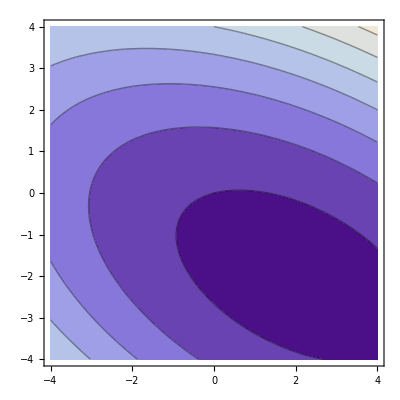

-Graphics3D-

-Graphics3D-

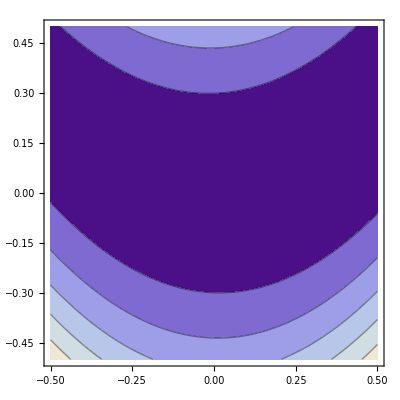

```mathematica
A = {{3,2},{2,6}};
b = {2,-8};
x = {x1,x2};

Rb = (1-z)^2 + 100(v-z^2)^2;
Cs =0.5*x.A.x - b.x
Plot3D[Cs, {x1, -4,4},{x2,-4,4}]
ContourPlot[Cs, {x1, -4,4},{x2,-4,4}]
Plot3D[Rb, {z, -1,1},{v,-1,1}]
bound = 0.5;
Plot3D[Rb, {z, -10,10},{v,-10,10}]
ContourPlot[Rb, {z,1.1,0.9},{v,1.1,0.9}]
```

```mathematica
{{-2 x1+1.5 x1^2,-2 x1+1. x1^2},{8 x2+1. x2^2,8 x2+3. x2^2}}
```

```mathematica
b1 = {1,2};
b2 = {3,4};
b1*b2
```

{3,8}

```mathematica
b2*b1
```

{3,8}

```mathematica
D[(1-x1^2)+100(x2-x1^2)^2,{{x1,x2},2}]
```

```mathematica
({{800 x1^2-400 (x2-x1^2)-2, -400 x1}, {-400 x1, 200}})
```

```mathematica
A = ({{a11, a12}, {a21, a22}});
b = ({{b1}, {b2}})
x = ({{x1, x2}});
1/2*x*A*x - b*x
```

Thread::tdlen: Objects of unequal length in 1/2\ {{x1, x2}}\ {{a11, a12}, {a21, a22}}\ {{x1, x2}} cannot be combined.

Thread::tdlen: Objects of unequal length in 1/2\ {{x1^2, x2^2}}\ {{a11, a12}, {a21, a22}} cannot be combined.

{{-b1 x1+1/2 {{x1^2,x2^2}} {{a11,a12},{a21,a22}},-b2 x2+1/2 {{x1^2,x2^2}} {{a11,a12},{a21,a22}}}}